```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy456-qmII"]
ClearAll[fs]
fs = Style[#, FontSize-> 16]&;
```

/Users/pjoot/project/figures/phy456-qmII

```mathematica
Manipulate[
Plot[
Sinc[ω t - Subscript[ω, 0]] + Sinc[ω t+Subscript[ω, 0]], 
{t, -r, r}, 
PlotRange->{-0.3,1.2},
PlotStyle-> Thick,
Ticks -> None
],{{r, 30},5,40}, {{Subscript[ω, 0], 28}, 1, 50}, {{ω, 2}, 1, 10}] (* /. {Subscript[ω, 0] -> 28, ω -> 2} *)
```

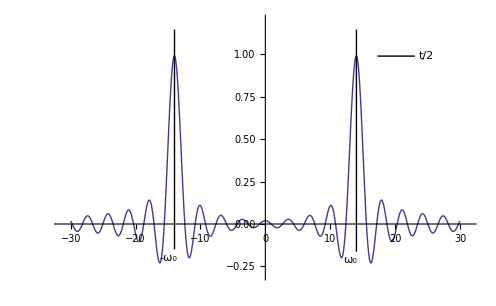

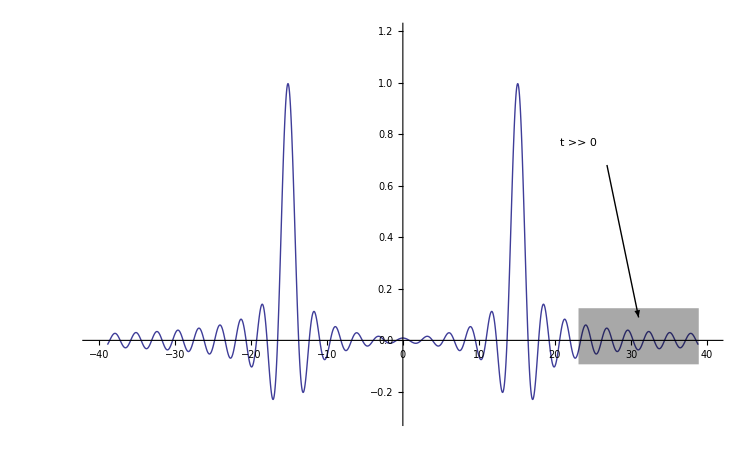

```mathematica
ClearAll[p, f]
f[w_, t_,w0_] := Sinc[(w - w0)t/2]+ Sinc[(w + w0)t/2]
(*p = With[{r = 30,ω0= 28,t = 2 },
Plot[
{
Callout[f[ω ,t, ω0], "(-ω_0, A_mi/ℏ)"//fs,{ -ω0, t/2}],
Callout[f[ω ,t, ω0], "(ω_0, A_mi/ℏ )"//fs,{ ω0, t/2}],
f[ω ,t, ω0]
}
, {ω, -2 ω0, 2 ω0}
, PlotRange->{{-2 ω0, 2 ω0 },{-.2t,.7t}}
,PlotStyle-> Thick
,Ticks -> None
]
];*)
g[w_, t_] := t/2
p = With[{r = 30,ω0= 28,t = 2 },
p1 = Plot[
{
Callout[g[ω, t], " A_mi/ℏ"//fs,{1.7 ω0, t/2}],
g[ω, t]
}
, {ω, -2 ω0, 2 ω0}
, PlotRange->{{-2 ω0, 2 ω0 },{-.2t,.7t}}
,PlotStyle-> Thick
,Ticks -> None
];
p2 = Plot[
{
Callout[f[ω ,t, ω0], "-ω_0" //fs,{ -ω0, t/2}],
Callout[f[ω ,t, ω0], "ω_0"//fs,{ ω0, t/2}],
f[ω ,t, ω0]
}
, {ω, -2 ω0, 2 ω0}
, PlotRange->{{-2 ω0, 2 ω0 },{-.2t,.7t}}
,PlotStyle-> Thick
,Ticks -> None
];
Show[{p1,p2}]
]
```

-Graphics-

```mathematica
peeters`exportForLatex["qmTwoL10fig3", p]
```

{qmTwoL10fig3.eps,qmTwoL10fig3pn.png}

```mathematica
ClearAll[p, f, qmTwoL10fig3]
f[omega_, omega0_, t_] := Sinc[ (omega  - omega0)t/2 ] + Sinc[(omega + omega0)t/2]
p[omega_, omega0_, r_] := Plot[
f[omega, omega0, t], 
{t, -r, r}, 
PlotRange->{-0.4,2},
PlotStyle-> {Thick,Black}]
(*Manipulate[
p[ω, Subscript[ω, 0], r],{{r, 10},5,40}, {{Subscript[ω, 0], 28}, 1, 50}, {{ω, 2}, 1, 10}
]*)
qmTwoL10fig3 = DynamicModule[{omega = 2, omega0 = 4, r = 5},
Show[{
p[omega, omega0, r],
Graphics[{
Text[MaTeX["\\omega_0"], {omega0, -0.3}]
}]
}]]
```

```mathematica
qmTwoR3fig1 = DynamicModule[{h = 2},
Show[{
Plot[ (h/10) (Sin[Pi x] + Sin[2 Pi x]), {x, 0, 2},
PlotRange-> {{-0.1, 2.1},{ -h/5, h + 0.2}},
Ticks -> None,
PlotStyle-> {Thick, Black},
Axes -> None
],
Graphics[{
Thick,
Arrow[{{0,0},{0,h}}],
Arrow[{{2,0},{2,h}}],
Line[{{0,0},{2,0}}],
Line[{{0,h/2},{2,h/2}}],
Text[MaTeX["0"], {0,-0.15}],
Text[MaTeX["a"], {2,-0.15}],
Text[MaTeX["E"], {1.5,h/2 +.1}]
}]
}]
]
```

```mathematica
peeters`exportForLatex["qmTwoR3fig1", qmTwoR3fig1]
```

{qmTwoR3fig1.eps,qmTwoR3fig1pn.png}

```mathematica
ClearAll[perp, qmTwoR3fig1]
perp[r_] := Module[{c},
c = (r // First) + I (r // Last);
c  = c / Norm[c];
c = c I;
{c // Re, c // Im} // N
]

qmTwoL11fig1 = DynamicModule[{o = {0,0},r = {2,3}, s = {2, -4}, a = {2, 0.5}, h = 5},
Graphics[{
Thick,
Arrowheads -> 0.08,
Arrow[{{0,0},{0,1}}],
Arrow[{{0,0},{1, 0}}],
Arrow[{o, r}],
Arrow[{r, r+ a}],
Arrow[{o, r + a}],
Arrow[{o, s}],
Arrow[{s, s+ a}],
Arrow[{o, s + a}],
Text[MaTeX["\\mathbf{r}"], r/2 + 0.25 perp[r]],
Text[MaTeX["\\mathbf{a}"], r + a/2 + 0.25 perp[a]],
Text[MaTeX["\\mathbf{r} + \\mathbf{a}"], (r+a)/2 - 0.4 perp[r+ a]],
Text[MaTeX["\\mathbf{s}"], s/2 - 0.25 perp[s]],
Text[MaTeX["\\mathbf{a}"], s + a/2 - 0.25 perp[a]],
Text[MaTeX["\\mathbf{s} + \\mathbf{a}"], (s+a)/2 + 0.4 perp[s+ a]]
}]

]
```

```mathematica
peeters`exportForLatex["qmTwoL11fig1", qmTwoL11fig1]
```

{qmTwoL11fig1.eps,qmTwoL11fig1pn.png}

```mathematica
ClearAll[rot, qmTwoL11fig3]

rot[r_] := Module[{c, th},
th = Pi/6;
c = (r // First) + I (r // Last);
c = c Exp[I th];
{c // Re, c // Im} // N
]
ang[r_] := ArcTan[ r // First, r // Last ]

qmTwoL11fig3 = DynamicModule[{o = {0,0},r = {3,1}, s = {3, -4}/2, h = 5, rr, rs, th1, th2},
rr = rot[r];
rs = rot[s];
th1 = ang[r];
th2 = ang[s];
Graphics[{

Arrow[{{0,0},{0,1}}],
Arrow[{{0,0},{1, 0}}],
Thick,
Arrowheads -> 0.08,
Arrow[{o, r}],
Arrow[{o, rr}],
Arrow[{o, s}],
Arrow[{o, rs}],

Text[MaTeX["\\mathbf{r}"], r/2 - 0.2 perp[r]],
Text[MaTeX["R(\\mathbf{r})"], rr/2 +0.2 perp[rr]],
Text[MaTeX["\\mathbf{s}"], s/2 - 0.2 perp[s]],
Text[MaTeX["R(\\mathbf{s})"], rs/2 +0.2 perp[rs]],
Text[MaTeX["\\mathbf{\\hat{n}}"], {-0.3, 0}],
Text[MaTeX["\\theta"], (r + rr)/2/5],
Text[MaTeX["\\theta"], (s + rs)/2/4],

Circle[o, 0.2],

(* circular arc with arrowhead: https://mathematica.stackexchange.com/a/257945/10 *)
Arrowheads[{.05}],
Arrow@ResourceFunction["SplineCircle"][{0,0},1,{1,0},{th1,th1 + Pi/6}],
Arrowheads[{.05}],
Arrow@ResourceFunction["SplineCircle"][{0,0},1,{1,0},{th2,th2 + Pi/6}]
}]
]
```

```mathematica
peeters`exportForLatex["qmTwoL11fig3", qmTwoL11fig3]
```

{qmTwoL11fig3.eps,qmTwoL11fig3pn.png}

```mathematica
ClearAll[qmTwoL18fig2]
qmTwoL18fig2 = DynamicModule[{o = {0,0},r = {3,1}, rr, th1 },
rr = rot[r];

th1 = ang[r];

Graphics[{

Arrow[{{0,0},{0,1}}],
Arrow[{{0,0},{1, 0}}],
Thick,
Arrowheads -> 0.08,
Arrow[{o, r}],
Arrow[{o, rr}],


Text[MaTeX["\\mathbf{r}"], r/2 - 0.2 perp[r]],
Text[MaTeX["R(\\mathbf{r})"], rr/2 +0.2 perp[rr]],

Text[MaTeX["\\theta"], (r + rr)/2/5],

(* circular arc with arrowhead: https://mathematica.stackexchange.com/a/257945/10 *)
Arrowheads[{.05}],
Arrow@ResourceFunction["SplineCircle"][{0,0},1,{1,0},{th1,th1 + Pi/6}]

}]
]
```

```mathematica
peeters`exportForLatex["qmTwoL18fig2", qmTwoL18fig2]
```

{qmTwoL18fig2.eps,qmTwoL18fig2pn.png}

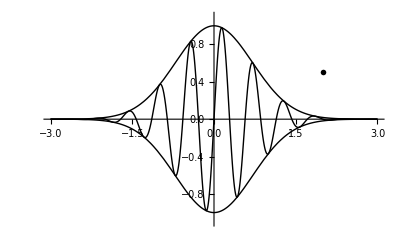

```mathematica
ClearAll[w, qmTwoL21Fig3, p, ws]
w[x_] := Exp[ -x^2 ]
ws[x_] := Sin[11 x] w[x]
p[w_, s_] := With[{r = 3},Plot[ s w[x], {x,-r, r}, PlotStyle-> {Thick, Black}, Ticks -> None, PlotRange-> {{-r, r}, {-1.1, 1.1}} ]]
qmTwoL21Fig3 = Show[{
p[w, 1], 
p[w,-1], 
p[ws, 1],
Graphics[{
Text[MaTeX["\psi(x, t = 0)"], {2, 0.5}]
}]
}]
```

```mathematica
peeters`exportForLatex["qmTwoL21Fig3", qmTwoL21Fig3]
```

{qmTwoL21Fig3.eps,qmTwoL21Fig3pn.png}

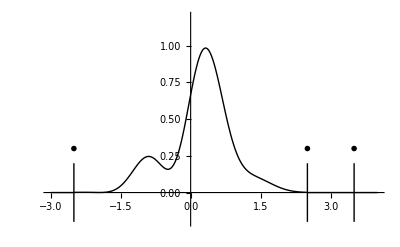

```mathematica
qmTwoL22fig1 = Show[{
Plot[
(HeavisideTheta[x+2.5] - HeavisideTheta[x-2.5])(2 + Sin[x] + Sin[4x]) Exp[-x^2]/3, {x, -3, 4},
Ticks -> None,
PlotStyle-> {Thick, Black},
PlotRange->{{-3, 4},{-0.2, 1.2}}
],
Graphics[{
Line[{{-2.5, -0.2},{-2.5, 0.2}}],
Line[{{2.5, -0.2},{2.5, 0.2}}],
Line[{{3.5, -0.2},{3.5, 0.2}}],
Text[MaTeX["x_1"], {-2.5, 0.3 }],
Text[MaTeX["x_2"], {2.5, 0.3 }],
Text[MaTeX["x_3"], {3.5, 0.3 }]
}]
}]
```

```mathematica
peeters`exportForLatex["qmTwoL22fig1", qmTwoL22fig1]
```

{qmTwoL22fig1.eps,qmTwoL22fig1pn.png}